## Задание №1

```mathematica
xs1={1,3,2,5.4,3.2,10,7.1,7.4,3.2,6.1,8.3,3.5,4,4.5,9,10.1,7.3,3.6,4.1}
```

{1,3,2,5.4,3.2,10,7.1,7.4,3.2,6.1,8.3,3.5,4,4.5,9,10.1,7.3,3.6,4.1}

```mathematica
xs2={0,1,1,2,2.6,2.6,2.6,3.1,4.6,4.6,6,6,7,9,9}
```

{0,1,1,2,2.6,2.6,2.6,3.1,4.6,4.6,6,6,7,9,9}

```mathematica
Clear[empiricalDistributionDensity]
empiricalDistributionDensity[xs_,deltaX_]:=Module[
{
varXS=Sort[xs],
n,intervalLen,intervals,values,labels
},
n=Round[Last[varXS]]+1;
intervalLen=N@(n/deltaX);
intervals=Partition[Table[i,{i,0,n,intervalLen}],2,1];
values=Table[Count[intervals⟦i,1⟧<=#≤intervals⟦i,2⟧&/@varXS,True],{i,deltaX}];
labels=StringJoin["[",ToString[#⟦1⟧],",",ToString[#⟦2⟧],")"]&/@intervals;
{values,BarChart[values,ChartLabels->labels,ImageSize->Medium]}
]
```

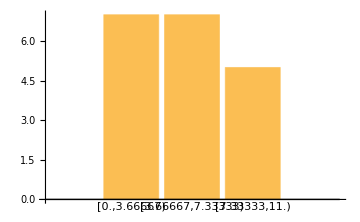
{{7,7,5},-Graphics-}

```mathematica
empiricalDistributionDensity[xs1,3]
```

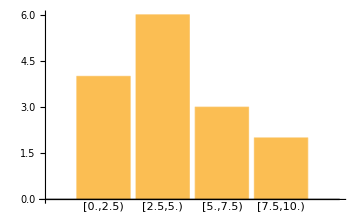
{{4,6,3,2},-Graphics-}

```mathematica
empiricalDistributionDensity[xs2,4]
```

## Задание №2

```mathematica
xs1
```

{1,3,2,5.4,3.2,10,7.1,7.4,3.2,6.1,8.3,3.5,4,4.5,9,10.1,7.3,3.6,4.1}

```mathematica
n=Length[xs1]
```

19

```mathematica
X=1/n Total[xs1]
```

5.41053

```mathematica
(#-X)^2&/@xs1
```

{19.4527,5.81064,11.6317,0.000110803,4.88643,21.0633,2.85432,3.95801,4.88643,0.475374,8.34906,3.65011,1.98958,0.829058,12.8843,21.9912,3.57011,3.27801,1.71748}

```mathematica
d2=1/n Total[(#-X)^2&/@xs1]
```

7.01463

```mathematica
S2=(n d2)/(n-1)
```

7.40433